```mathematica
a=0; b=6;n=10;
h=(b-a)/n;
XData={}; YouData={};
For[i=0,i≤n,i++,
x1data[i]=N[a+i*h];
y1data[i]=N[x1data[i]/(Sqrt[1+x1data[i]^2+Sqrt[(1+x1data[i]^2)^3]])];
XData=Append[XData,x1data[i]];
YouData=Append[YouData,y1data[i]];];
MatrixForm[XData]
MatrixForm[YouData]
```

(0.
0.6
1.2
1.8
2.4
3.
3.6
4.2
4.8
5.4
6.)

(0.
0.349569
0.479946
0.499794
0.486504
0.465003
0.442731
0.421868
0.402935
0.385918
0.370637)

```mathematica
data1:={{0.,0.},{0.6,0.349569461002367},{1.2,0.4799461783270176},{1.8,0.49979383206964295},{2.4,0.4865042554105199},{3.,0.465002974202142},{3.6,0.4427308730636989},{4.2,0.4218678212858997},{4.8,0.40293537489480663},{5.4,0.38591807616198465},{6.,0.37063723541804355}}
gr[x_]=Fit[data1,{1,x},x]
```

0.320086+0.0237564 x

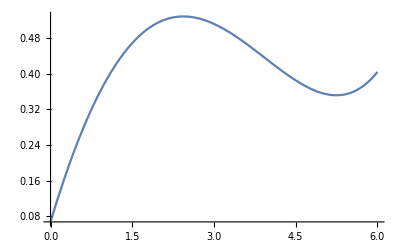

```mathematica
Plot[gr[x],{x,0,6}]
```

```mathematica
gr1:=Plot[N[x/(Sqrt[1+x^2+Sqrt[(1+x^2)^3]])],{x,0,6}]
gr2:=Plot[gr[x],{x,0,6}]
gr3:=ListPlot[Table[{N[x1data[i]],N[y1data[i]]},{i,0,n}]]
```

```mathematica
For[i=0,i≤n,i++,
SumData[i]=N[gr[x1data[i]]];];
```

SumData

```mathematica
sum=∑_(i=0)^n (SumData[i]-y1data[i])^2
```

0.170804